```mathematica
(*Initialisation - Run first*)
SetEnvironment["OMP_NUM_THREADS"->"8"]
(*Replace the following with the appropriate pathways for your device*)
Import["/Users/questuser/Documents/QuESTlink/Link/QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["/Users/questuser/Documents/Kathryn/quest_link"]; (*Creating QuEST environment*)
Import["/Users/questuser/Documents/Kathryn/RydbergInstaSWAPGerardCZ.wl"]; (*Configuration File*)
data=Import["/Users/questuser/Documents/Kathryn/SU4Gates9Qubits.csv"]; (*Imported gates from Qiskit*)
userconfig=<|
NQubits-> 9,
QubitLocations->Association[#1->#2&@@@Transpose@{Range[0,8],Flatten[Table[{i,j,k},{i,0,2},{j,0,2},{k,0,0}],2]}],
(* blockade radius in μm*)
BlockadeRadius->Sqrt[2],
(* inter-atomic separation in μm. This will be the unit of the lattice given in qubitLocations *)
UnitLattice->1,
(* T1=τvac/nqubits in μs *)
VacuumLifeTime->4*10^6,
(* the γ noise on theq initialization *)
LeakProbInit->0.007,
(* duration on the initialization *)
DurInit->300,
(* measurement induces atom loss afterward *)
FidMeas-> 100,
DurMeas-> 2*10^4,
(* the increasing chance of atom loss due to measurement, in percent *)
AtomLossMeas-> 0,
(* mostly used in the single qubit noise, unit μs. It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.49*10^6,
(* leak probability of implementing multi-qubit gates *)
LeakProbCZ-> <|01-> 0.001,11->0.001 |>,
(* Rabi frequency, MHz *)
Ω->1,
(* fidelity of swap operation *)
FidSWAP->99.7
|>;
RydDev=CreateRydbergDevice[userconfig];
RydDev[InitLocations]
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations];
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
```

-Graphics3D-

```mathematica
Fraction[a_,b_]:=a/b
KetList[NQ_]:=Table[i,{i,0,2^NQ-1,1}]
(*Fully Translate Qiskit output into QuEST format, SWAP Procedure*)
SU4Gate[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP], a[[1]],a[[2]]],Subscript[CZ, a[[2]],a[[1]]][Pi]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]

(*SU4Gate[data[[400;;1000]][[112]],0,1]*)

(*Generate a list of random permutations of NQ qubits*)
NRandQbits[NQ_]:=RandomSample[Range[0,NQ-1],NQ]

(*Compute the probability of getting a heavy output of the model circuit from the noisy circuit THIS STILL AIN'T RIGHT*)
CheckHeavyOutputProb[PoutcomesIMPLEMENTED_,PoutcomesMODEL_]:=Pick[PoutcomesIMPLEMENTED,Table[If[PoutcomesMODEL[[i]]>=Median[PoutcomesMODEL],True,False],{i,1,Length[PoutcomesMODEL]}]];

(*Generate a layer of gates for building a QV circuit*)
QVLayer[DataSet_,NQ_,RQs_,i_]:=Table[If[blockadeCheck[{RQs[[n]],RQs[[n+1]]}],LayerCirc=SU4Gate[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]],LayerCirc=Flatten[Join[Join[{Subscript[SWAP, RQs[[n+1]],4]},SU4Gate[DataSet[[n+i]],RQs[[n]],4]],{Subscript[SWAP, RQs[[n+1]],4]}]]]; LayerCirc,{n,1,2*Quotient[NQ,2],2}];
(*Generate initialisation layer of circuit*)
InitCirc[Reg_,MaxNQ_]:=Table[Subscript[Init, b],{b,0,MaxNQ-1,1}]

(*Generate circuit of m=d layers of SU(4) gates*)
QVCirc[DataSet_,NQ_]:=Table[RQS=NRandQbits[NQ];Layer=QVLayer[DataSet,NQ,RQS,i];
(*Print["# Qubits, ",NQ," # Gates per Layer, ",Length[Layer]]*);Flatten[Layer],{i,0,NQ-1,1}]

(*Generating and applying the circuits to a register and getting the probability of a heavy output*)
QVProcedure[DataSet_,NQ_, MaxNQ_,NReps_,Reg_]:=Table[
Circ1=QVCirc[DataSet[[NQ*Quotient[NQ,2]*Rep+1;;NQ*Quotient[NQ,2]*(Rep+1)]],NQ];
Initialisation=InitCirc[Reg,MaxNQ];
InitCircuit=Flatten[Join[Initialisation,Circ1]];
CircNoisy=ExtractCircuit[InsertCircuitNoise[InitCircuit,RydDev,ReplaceAliases->True]];
CircModel=ExtractCircuit[GetCircuitSchedule[Circ1,RydDev,ReplaceAliases->True]];
SetQuregMatrix[Reg,RandomMixState[MaxNQ]];
ApplyCircuit[Reg,CircNoisy];
PoutcomesNoisy=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
(*Print[PoutcomesNoisy];*)
InitZeroState[Reg];
(*Print[DrawCircuit[CircModel]];*)
ApplyCircuit[Reg,CircModel];
PoutcomesModel=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
(*Print[NQ, " Model Outcomes Probabilities ",PoutcomesModel," Noisy Outcome Probabilities ",PoutcomesNoisy];*)
HeavyOutputs=CheckHeavyOutputProb[PoutcomesNoisy,PoutcomesModel];
Total[HeavyOutputs],{Rep,0,NReps-1,1}]


(*Put everything together and get a value for Quantum Volume*)
QVCalc[DataSet_,MaxNQ_,NReps_]:=Table[ρ=CreateDensityQureg[MaxNQ];
HOP=QVProcedure[DSSplice=DataSet[[(Total[Table[a*Quotient[a,2],{a,0,NQ-1}]]*NReps)+1 ;;Total[Table[a*Quotient[a,2],{a,0,NQ}]*NReps]]],NQ,MaxNQ,NReps,ρ];
MHOP=Mean[HOP];
σ=StandardDeviation[HOP]/Sqrt[NReps-1];;
If[ Re[(MHOP-2σ)]>2/3,VQ=2^NQ,VQ=0];
Print[{"Layer",NQ,VQ}];
{NQ,MHOP±2σ}
,{NQ,2,MaxNQ,1}];
InstaSWAPQV=AbsoluteTiming[QVCalc[data,9,200]];
Print["Quantum Volume = ",Max[InstaSWAPQV[[2]]]," Time Taken ", InstaSWAPQV[[1]] ]
Print[InstaSWAPQV[[2]]]
DestroyAllQuregs[];
```

{Layer,2,4}

{Layer,3,8}

{Layer,4,16}

{Layer,5,32}

{Layer,6,64}

{Layer,7,128}

{Layer,8,256}

{Layer,9,0}

Quantum Volume = Max[9,0.660502±0.00124035,0.672789±0.00145219,0.720973±0.00245386,0.725693±0.0033095,0.735547±0.0125194,0.755296±0.00678135,0.756456±0.00490247,0.775987±0.0101676] Time Taken 11100.7

{{2,0.735547±0.0125194},{3,0.775987±0.0101676},{4,0.755296±0.00678135},{5,0.756456±0.00490247},{6,0.725693±0.0033095},{7,0.720973±0.00245386},{8,0.672789±0.00145219},{9,0.660502±0.00124035}}

```mathematica
Import["/Users/questuser/Documents/Kathryn/RydbergGerardCZDCSWAP.wl"];
SWAPQV=AbsoluteTiming[QVCalc[data,9,200]];
Print["Quantum Volume = ",Max[SWAPQV[[2]]]," Time Taken ", SWAPQV[[1]] ]
Print[SWAPQV[[2]]]
DestroyAllQuregs[];
```

{Layer,2,4}

{Layer,3,8}

{Layer,4,16}

{Layer,5,32}

{Layer,6,64}

{Layer,7,128}

{Layer,8,256}

{Layer,9,0}

Quantum Volume = Max[9,0.6614±0.00110686,0.672152±0.00137227,0.720146±0.00214075,0.726366±0.00322184,0.734657±0.0126647,0.757581±0.00667702,0.760419±0.00484592,0.793794±0.0109541] Time Taken 11191.6

{{2,0.734657±0.0126647},{3,0.793794±0.0109541},{4,0.757581±0.00667702},{5,0.760419±0.00484592},{6,0.726366±0.00322184},{7,0.720146±0.00214075},{8,0.672152±0.00137227},{9,0.6614±0.00110686}}

$Aborted

Quantum Volume = Max[9,0.630928±0.00113118,0.648287±0.00122767,0.706867±0.00260168,0.713787±0.00288264,0.739286±0.0119628,0.750242±0.00663144,0.757052±0.00469813,0.780432±0.0110546] Time Taken 10715.6

{{2,0.739286±0.0119628},{3,0.780432±0.0110546},{4,0.750242±0.00663144},{5,0.757052±0.00469813},{6,0.713787±0.00288264},{7,0.706867±0.00260168},{8,0.648287±0.00122767},{9,0.630928±0.00113118}}

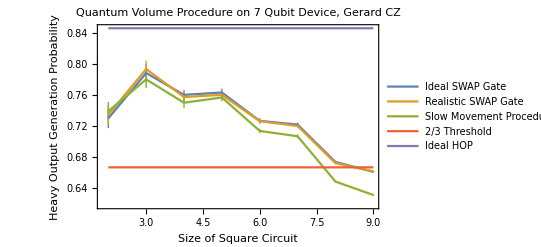

```mathematica
userconfig=<|
NQubits-> 9,
QubitLocations->Association[#1->#2&@@@Transpose@{Range[0,8],Flatten[Table[{i,j,k},{i,0,2},{j,0,2},{k,0,0}],2]}],
(* blockade radius in μm*)
BlockadeRadius->3,
(* inter-atomic separation in μm. This will be the unit of the lattice given in qubitLocations *)
UnitLattice->1,
(* T1=τvac/nqubits in μs *)
VacuumLifeTime->4*10^6,
(* the γ noise on theq initialization *)
LeakProbInit->0.007,
(* duration on the initialization *)
DurInit->300,
(* measurement induces atom loss afterward *)
FidMeas-> 100,
DurMeas-> 2*10^4,
(* the increasing chance of atom loss due to measurement, in percent *)
AtomLossMeas-> 0,
(* mostly used in the single qubit noise, unit μs. It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.49*10^6,
(* leak probability of implementing multi-qubit gates *)
LeakProbCZ-> <|01-> 0.001,11->0.001 |>,
(* Rabi frequency, MHz *)
Ω->1,
(* fidelity of swap operation *)
FidSWAP->99.7
|>;
RydDev=CreateRydbergDevice[userconfig];

SU4Gate[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP], a[[1]],a[[2]]],{Subscript[CZ, a[[2]],a[[1]]][Pi],Subscript[Wait, Range[0,userconfig[NQubits]-1][[All]]][500]}],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]

MoveQV=AbsoluteTiming[QVCalc[data,9,200]];
Print["Quantum Volume = ",Max[MoveQV[[2]]]," Time Taken ",MoveQV[[1]] ]
Print[MoveQV[[2]]]

IdealHOP=Table[{i,(1+Log[2])/2},{i,2,9}];
Thresh=Table[{i,2/3},{i,2,9}];
ListLinePlot[{InstaSWAPQV[[2]],SWAPQV[[2]],MoveQV[[2]],Thresh,IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Generation Probability]},PlotLabel->"Quantum Volume Procedure on 7 Qubit Device, Gerard CZ",Frame->True,FrameLabel->{"Size of Square Circuit","Heavy Output Generation Probability"},PlotLegends->{"Ideal SWAP Gate","Realistic SWAP Gate","Slow Movement Procedure","2/3 Threshold","Ideal HOP"}]
DestroyAllQuregs[];
```

```mathematica
InstaSWAPQV
```

{11062.2,{{2,0.730064±0.0126733},{3,0.788706±0.0114448},{4,0.760433±0.00610512},{5,0.763468±0.00493037},{6,0.726783±0.00329315},{7,0.721943±0.00239884},{8,0.673599±0.00149345},{9,0.660917±0.00104238}}}

```mathematica
InstaHOP={{2,0.7355469906511872±0.01251944143181066},{3,0.775987181777516±0.010167585585215853},{4,0.755295944237123±0.00678135072831472},{5,0.7564555356216991±0.004902470443749478},{6,0.725692784944827±0.0033095027066361456},{7,0.7209730481478179±0.0024538565415231223},{8,0.672789301939968±0.0014521884189475965},{9,0.6605016117290387±0.0012403527828113265}}

SWAPHOP={{2,0.736428±0.0131019},{3,0.775987181777516±0.010167585585215853},{4,0.757936±0.00674214},{5,0.743349±0.00516281},{6,0.689238±0.00351049},{7,0.662192±0.00303179},{8,0.590931±0.00269218},{9,0.558019±0.00236677}}

MoveHOP={{2,0.7350610390785006±0.012082910117828034},{3,0.7775680250277653±0.012128178070968875},{4,0.7522643848570192±0.006527399761331977},{5,0.7568171851154704±0.00484302238532501},{6,0.7166324179371205±0.0029801547002349734},{7,0.7054947114091317±0.00247247983522516},{8,0.6478753567796238±0.0014010481703297425},{9,0.6299564171412708±0.0011451044791867247}}(*{{2,0.7326362774844749±0.012155715254343901},{3,0.7807522065786893±0.01090089556815594},{4,0.7606362600308175±0.005792652296324362},{5,0.764640909015542±0.004827136032972652},{6,0.7247692066544223±0.003333611255014028},{7,0.7166149768410187±0.002314012013008267},{8,0.6673799360681116±0.0016026172605102514},{9,0.6536909390220549±0.0011792138870591567}}*)
```

{{2,0.735547±0.0125194},{3,0.775987±0.0101676},{4,0.755296±0.00678135},{5,0.756456±0.00490247},{6,0.725693±0.0033095},{7,0.720973±0.00245386},{8,0.672789±0.00145219},{9,0.660502±0.00124035}}

{{2,0.736428±0.0131019},{3,0.775987±0.0101676},{4,0.757936±0.00674214},{5,0.743349±0.00516281},{6,0.689238±0.00351049},{7,0.662192±0.00303179},{8,0.590931±0.00269218},{9,0.558019±0.00236677}}

{{2,0.735061±0.0120829},{3,0.777568±0.0121282},{4,0.752264±0.0065274},{5,0.756817±0.00484302},{6,0.716632±0.00298015},{7,0.705495±0.00247248},{8,0.647875±0.00140105},{9,0.629956±0.0011451}}

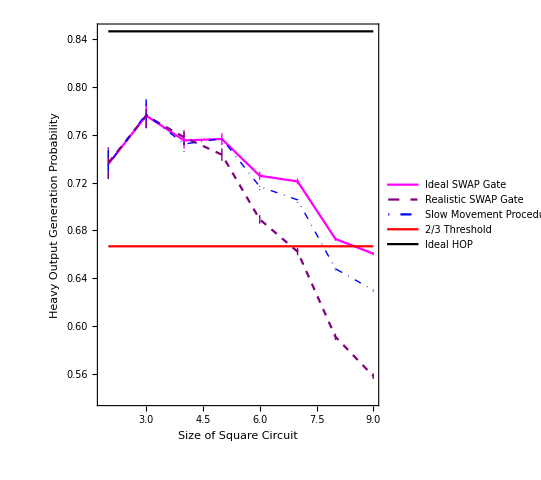

```mathematica
IdealHOP=Table[{i,(1+Log[2])/2},{i,2,9}];
Thresh=Table[{i,2/3},{i,2,9}];
ListLinePlot[{InstaHOP,SWAPHOP,MoveHOP,Thresh,IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Generation Probability]},(*PlotLabel->"Quantum Volume Procedure on 7 Qubit Device, Gerard CZ",*)PlotStyle->{Magenta,{Purple,Dashed},{Blue,Thick,DotDashed},Red,Black},Frame->True,FrameLabel->{"Size of Square Circuit","Heavy Output Generation Probability"},AspectRatio->1.2/1,PlotLegends->Placed[{"Ideal SWAP Gate","Realistic SWAP Gate","Slow Movement Procedure 500μs","2/3 Threshold","Ideal HOP"},{Left,Bottom}]]
```